## Scène 2D

### Paramètres

```mathematica
nbPixels =32;     (* Nombre de pixels par image *)
nbImages = 30;    (* Nombre d'images pour l'entrainement du réseau *)
nbTestImages = 20;    (* Nombre d'images pour les tests du réseau *)
nbDimPos = 2;    (* Nombre d'encodage de la position d'un point dans le réseau *)
nbDimDir = 0;      (* Nombre d'encodage de la direction d'un rayon dans le réseau *)
nbSamples = 64;  (* Nombre d'échantillon le long d'un rayon pour l'entrainement du réseau *)
layerDim = 32;    (* Dimension des layers des réseaux *)
```

### Fonctions utiles

```mathematica
e2p[v_]:=Append[v,1];
p2e[v_]:=Delete[v,-1]/v[[-1]];
(* remplace  {{0,c},{0,c},{0.5,c},{0.5,c},.... -> {0, c},{0, c},{0.5, c},{0, c}  *)
ajuste[f_]:=Block[{k},(
k=First[Position[(#>0)&/@f[[All,1]],True]/.{}->{{0}}][[1]];
N@Table[{If[i>k,0.,f[[i,1]]],f[[i,2]]},{i,1,Length[f]}]
)];
(* Ajoute une densité à une couleur *)
rgb2rgba[{a_,RGBColor[r_,g_,b_]}]:=RGBColor[r,g,b,a];
(* Mixe une couleur avec une autre couleur si l'intensité de la première couleure est inférieur à 1 *)
myBlend[{currentAlpha_,currentColor_},{_,_}]:={1.,currentColor}/;(currentAlpha>=1.);
myBlend[{currentAlpha_,RGBColor[ra_,ga_,ba_]},{newAlpha_,RGBColor[rb_,gb_,bb_]}]:=Block[{na},(
na=Min[1-currentAlpha,newAlpha];
{currentAlpha+na,RGBColor[
(currentAlpha*ra+na*rb)/(currentAlpha+na),
(currentAlpha*ga+na*gb)/(currentAlpha+na),
(currentAlpha*ba+na*bb)/(currentAlpha+na)]
}
)];

(* Affichage camera *)
afficheCam[m_,d_,imin_,imax_,num_]:=Block[{mi,pos,p1,p2},(
mi=Inverse[m];
pos=p2e[(mi.{0,0,1})];
p1=p2e[(mi.{imin*d,d,1})];
p2=p2e[(mi.{imax*d,d,1})];
Graphics[{
PointSize[0.02],Point[pos],
Line[{pos,p1}],Line[{pos,p2}],
Thick,Line[{p1,p2}],
Text[Style[num,24],pos + (p1 + p2) / Norm[p1 + p2]]
}]
)];
afficheCam[m_,d_,imin_,imax_]:=afficheCam[m,d,imin,imax,""];
```

### Définition d’une camera 2D projective tel que M = K R T : 3x3

```mathematica
camera[f_,cx_,a_,{tx_,ty_}]:=Block[{k,r,t},(
k={{f,cx,0},{0,1,0},{0,0,1}};
r=TransformationMatrix[RotationTransform[a]];
t=TransformationMatrix[TranslationTransform[{tx,ty}]];
k.r.t
)];
```

### Affichage des caméras dans le monde 2D

#### Création des caméra

```mathematica
cams=Table[camera[nbPixels/2, nbPixels/2,a+Pi/2,{Cos[a],-Sin[a]}*RandomReal[{5.2,5.5}]],{a,0,2Pi-0.1,2*Pi/nbImages}];
camsShow=Show[
Table[afficheCam[cams[[i]],1,0, nbPixels,i],{i,1,Length[cams]}]
];
```

### Création d’une projection de points à partir de chaque caméra

```mathematica
lignePoints[m_,x_,dmin_,dmax_,dstep_]:=Block[{mi,g},(
g=Range[dmin,dmax,dstep];
mi=Inverse[m];
p2e[(mi.{x,1,1/#})]&/@g

)]
```

### Création et rendu d’une scène 2D

#### Définition de scène dans un espace de 3x3

```mathematica
(*scene = {sphere[{-2.5,-2.5},0.5,RGBColor[0.7207624921030475, 0.8783226707518454, 0.3998020771432411],0.47121369504218],sphere[{-2.5,-1.5},0.5,RGBColor[0.3109350801732389, 0.7743896071911034, 0.060229313508623816],0.5650706487802224],sphere[{-2.5,-0.5},0.5,RGBColor[0.6592167986516495, 0.5637775819431217, 0.1460028216169662],0.6655200329304803],sphere[{-2.5,0.5},0.5,RGBColor[0.8835355712985848, 0.3489798799262902, 0.16240512089788006],0.9430793300865326],sphere[{-2.5,1.5},0.5,RGBColor[0.7731678670776276, 0.7416520875871704, 0.5602580523967331],0.7801181775079864],sphere[{-2.5,2.5},0.5,RGBColor[0.7336632502452687, 0.7108376095402236, 0.20243179376558706],0.41207927651048004],sphere[{-1.5,-2.5},0.5,RGBColor[0.22079957329800015, 0.8212586923763179, 0.9859747050943295],0.6390572007658623],sphere[{-1.5,-1.5},0.5,RGBColor[0.5937174112315127, 0.6257636178866732, 0.8807674184203331],0.9577171292822035],sphere[{-1.5,-0.5},0.5,RGBColor[0.7004783836851922, 0.282759087996435, 0.8717243877688112],0.9781286409433176],sphere[{-1.5,0.5},0.5,RGBColor[0.3981820345449698, 0.1425757782837591, 0.2956213492640949],0.5297798666793608],sphere[{-1.5,1.5},0.5,RGBColor[0.07321687360816664, 0.07299558675734219, 0.2767077464562149],0.4891075882119096],sphere[{-1.5,2.5},0.5,RGBColor[0.46158753863332436, 0.4356390012988107, 0.2124445633045542],0.7952992189521437],sphere[{-0.5,-2.5},0.5,RGBColor[0.8413167761444262, 0.029357736220502417, 0.7337277254218217],0.9102495537174884],sphere[{-0.5,-1.5},0.5,RGBColor[0.17339491436813548, 0.7644658909874773, 0.39928777865095766],0.9133468848913857],sphere[{-0.5,-0.5},0.5,RGBColor[0.6208579306809776, 0.33643407484417254, 0.2897083107917262],0.6348167767029302],sphere[{-0.5,0.5},0.5,RGBColor[0.7254456829404325, 0.6384279928047414, 0.38700412177737564],0.7325175178096426],sphere[{-0.5,1.5},0.5,RGBColor[0.19336606166334547, 0.9881485706550515, 0.9717211206872236],0.8052380398967394],sphere[{-0.5,2.5},0.5,RGBColor[0.44445446657869936, 0.9494675881936523, 0.13186592587421053],0.960610743107327],sphere[{0.5,-2.5},0.5,RGBColor[0.02141115306732022, 0.7304483180786456, 0.820364709361038],0.4117343122141274],sphere[{0.5,-1.5},0.5,RGBColor[0.7927485372974363, 0.8179703382184174, 0.8812002392361054],0.7683568283407547],sphere[{0.5,-0.5},0.5,RGBColor[0.8380159669485854, 0.39859913711780526, 0.22178864553044386],0.8209077273448029],sphere[{0.5,0.5},0.5,RGBColor[0.721777836234579, 0.6123620112559844, 0.16961772139810716],0.5144917067353431],sphere[{0.5,1.5},0.5,RGBColor[0.2657848823298312, 0.05861551721069391, 0.08764680716320017],0.8945558656792094],sphere[{0.5,2.5},0.5,RGBColor[0.8905309773118286, 0.2025263744665775, 0.014477165305500694],0.6461763934604484],sphere[{1.5,-2.5},0.5,RGBColor[0.3331143330728983, 0.5115421560916895, 0.030245862476348417],0.4221014987445021],sphere[{1.5,-1.5},0.5,RGBColor[0.3379784202326863, 0.35077519840922444, 0.44277472333864165],0.945273862832569],sphere[{1.5,-0.5},0.5,RGBColor[0.047800941077301484, 0.4444448190244743, 0.5548952868316601],0.4320756901071485],sphere[{1.5,0.5},0.5,RGBColor[0.3429823903412532, 0.6893874316922914, 0.5645316678934469],0.4480191221770765],sphere[{1.5,1.5},0.5,RGBColor[0.010221230554417815, 0.3515727529316166, 0.639849747208322],0.5734971814900679],sphere[{1.5,2.5},0.5,RGBColor[0.5022620704486644, 0.1693210558056324, 0.5449727349686417],0.4159951339957392],sphere[{2.5,-2.5},0.5,RGBColor[0.8902005657316616, 0.9564417871695916, 0.9485602614805757],0.9603315040592917],sphere[{2.5,-1.5},0.5,RGBColor[0.29778480990955924, 0.8226968714292366, 0.14557770403912795],0.9979943355411247],sphere[{2.5,-0.5},0.5,RGBColor[0.42271188026322193, 0.05725543452113069, 0.6897901577462249],0.8929942984296451],sphere[{2.5,0.5},0.5,RGBColor[0.5425693383570978, 0.9548663239204644, 0.14117635083346403],0.6277755489770713],sphere[{2.5,1.5},0.5,RGBColor[0.8617128317327118, 0.8998878802619963, 0.33860399394221763],0.6153480311174954],sphere[{2.5,2.5},0.5,RGBColor[0.5640261464947385, 0.9228624694678265, 0.03994076988441009],0.6498253164399784]};*)
(*scene = {sphere[{-2.5,-2.5},0.5,RGBColor[0.21201029355193812, 0.8511569217110755, 0.5725958735529311],1],sphere[{-2.5,-1.5},0.5,RGBColor[0.8671981680231289, 0.8511036838622881, 0.5050813110026788],1],sphere[{-2.5,-0.5},0.5,RGBColor[0.9433903159544126, 0.3690983263368277, 0.41295513394993266],1],sphere[{-2.5,0.5},0.5,RGBColor[0.9795026855811626, 0.18473347924540717, 0.5949163496445826],1],sphere[{-2.5,1.5},0.5,RGBColor[0.18512925801058344, 0.23918351023918571, 0.8217857177935468],1],sphere[{-2.5,2.5},0.5,RGBColor[0.6621065361884215, 0.840062915896651, 0.7914405857772384],1],sphere[{-1.5,-2.5},0.5,RGBColor[0.20554490461587083, 0.5301772156352804, 0.13912935613221888],1],sphere[{-1.5,-1.5},0.5,RGBColor[0.3178746690652141, 0.8168004418150117, 0.019619701696883762],1],sphere[{-1.5,-0.5},0.5,RGBColor[0.33531814486726486, 0.11175219902624267, 0.6504417330162424],1],sphere[{-1.5,0.5},0.5,RGBColor[0.9923138961932243, 0.27940026471537305, 0.21306007420117745],1],sphere[{-1.5,1.5},0.5,RGBColor[0.2975309612828114, 0.0735236797533887, 0.900953247281068],1],sphere[{-1.5,2.5},0.5,RGBColor[0.43691487257825146, 0.36844981729166615, 0.049871865277819394],1],sphere[{-0.5,-2.5},0.5,RGBColor[0.8844581993474663, 0.041978794619627946, 0.680213342473355],1],sphere[{-0.5,-1.5},0.5,RGBColor[0.8943008510479908, 0.6402842538302538, 0.7358349646497329],1],sphere[{-0.5,-0.5},0.5,RGBColor[0.09811649177192971, 0.45988430169560246, 0.7005187812584266],1],sphere[{-0.5,0.5},0.5,RGBColor[0.43943349780100616, 0.012002210254431267, 0.9654686204521921],1],sphere[{-0.5,1.5},0.5,RGBColor[0.8849910427403465, 0.43769301967229035, 0.9615880392800698],1],sphere[{-0.5,2.5},0.5,RGBColor[0.6024101903000856, 0.18060806695240994, 0.757533617562159],1],sphere[{0.5,-2.5},0.5,RGBColor[0.6334048901392528, 0.8557566483808341, 0.538300674594731],1],sphere[{0.5,-1.5},0.5,RGBColor[0.9575281678632801, 0.7541796873404294, 0.30410846304242023],1],sphere[{0.5,-0.5},0.5,RGBColor[0.7242921441042252, 0.5726266191849712, 0.9906366764280223],1],sphere[{0.5,0.5},0.5,RGBColor[0.9350901418355082, 0.13193421036082964, 0.020465487476080124],1],sphere[{0.5,1.5},0.5,RGBColor[0.4316524083139297, 0.11270457160224945, 0.7453986941181034],1],sphere[{0.5,2.5},0.5,RGBColor[0.6908315582397686, 0.8116177771234478, 0.9199258339467242],1],sphere[{1.5,-2.5},0.5,RGBColor[0.693016873737438, 0.8214368216624257, 0.09846880331053143],1],sphere[{1.5,-1.5},0.5,RGBColor[0.39964503872125423, 0.14900264143158903, 0.21756036703326953],1],sphere[{1.5,-0.5},0.5,RGBColor[0.8745508600166998, 0.4719865570867714, 0.5328940571764449],1],sphere[{1.5,0.5},0.5,RGBColor[0.4592412493244271, 0.9749886144990376, 0.13921237872774328],1],sphere[{1.5,1.5},0.5,RGBColor[0.8480179696841283, 0.8756053974036968, 0.2511123153189645],1],sphere[{1.5,2.5},0.5,RGBColor[0.4217385191431553, 0.07282920449513663, 0.8874026442149294],1],sphere[{2.5,-2.5},0.5,RGBColor[0.8862175064846161, 0.757175810716836, 0.11028700679218817],1],sphere[{2.5,-1.5},0.5,RGBColor[0.44131967346125234, 0.44599008143151897, 0.7754627434568881],1],sphere[{2.5,-0.5},0.5,RGBColor[0.641883516126659, 0.14122046551223089, 0.6667627129847387],1],sphere[{2.5,0.5},0.5,RGBColor[0.32651655862088225, 0.5810222876833253, 0.6446794815575616],1],sphere[{2.5,1.5},0.5,RGBColor[0.3231928665978787, 0.4136203097979054, 0.4116779855961181],1],sphere[{2.5,2.5},0.5,RGBColor[0.6462786831220035, 0.6879542368265801, 0.8875615238240258],1]};*)
scene={
sphere[{0,0},2,Blue,1],
sphere[{-2,-2},1,Red,1],
sphere[{2,2},1,Cyan,1],
sphere[{2,-2},1,Green,1],
sphere[{-2,2},1,Yellow,1]
};
```

#### Affichage de la scène

```mathematica
axes =Graphics[{
Thick,
Red,Arrow[{{0,0},{2,0}}],
Green,Arrow[{{0,0},{0,2}}]
}];
boundingBox = {
Line[{{-3., -3.}, {3. ,-3.}}],
Line[{{-3., -3.}, {-3., 3.}}],
Line[{{3., 3.}, {3., -3.}}],
Line[{{-3., 3.}, {3., 3.}}]
};
boudingBoxGraphics = Graphics[{
EdgeForm[Dashed],Transparent, Rectangle[{3, 3}, {-3, -3}]
}];
rendu[sphere[{cx_,cy_},r_,c_,α_]]:={Opacity[α],c,Disk[{cx,cy},r]};
rendu[sphere[{cx_,cy_},r_,c_,α_],{x_,y_}]:=Block[{d},(
d=Norm[{x,y}-{cx,cy}];
If[(d<=r),{α,c},{0,c}]
)];
rendu[scene_]:=Graphics[rendu/@scene];
rendu[scene_,m_,x_,dmin_,dmax_]:=Block[{p,t,j},(
p=lignePoints[m,x,dmin,dmax,0.1];
t=Table[rendu[scene[[i]],#]&/@p,{i,1,Length[scene]}];
j=Flatten[Transpose[ajuste/@t]/.({0.,_}->Nothing),1];
rgb2rgba[Fold[myBlend,{0.,RGBColor[0,0,0]},j]]
)];
```

### Visualisation du processus de rendu

```mathematica
Manipulate[(
p = lignePoints[cams[[1]],x,0.5,8,0.1];
Show[
afficheCam[cams[[1]],1,0,nbPixels,1],
boudingBoxGraphics,
rendu[scene],
Graphics[Point[p]]]
),{x,0,nbPixels}];
```

### Rendu d’image 2D à partir de chaque caméra

```mathematica
images = ParallelTable[rendu[scene, cams[[i]], #, 1, 8]&/@Range[0, nbPixels], {i, 1, Length[cams]}];
```

```mathematica
rgb=Table[(List@@#)&/@images[[i,All,1;;3]],{i,1,Length[images]}];
Image[rgb, ImageSize->500]
```

-Graphics-

## Partie NeRF

### Échantillonnage des points

```mathematica
samplePoints[line_, boundingBox_, numPoints_] := Block[
{lineSection, intersections},
lineSection = InfiniteLine[line];
intersections = DeleteCases[Table[RegionIntersection[lineSection, boundingBox[[i]]], {i, 1, 4}],EmptyRegion[__]];
If[Length[intersections] > 1, Block[
{sp,a,b, p1, p2, d1, d2},
p1=intersections[[1,1,1]];
p2=intersections[[2,1,1]];
d1 = EuclideanDistance[p1, line[[1]]];
d2 = EuclideanDistance[p2, line[[1]]];
a =If[d1<d2, p1, p2];
b=If[d1<d2, p2, p1];
sp=Table[a+(i/(numPoints-1)) (b-a),{i,0,numPoints-1}] ;
sp
],{} ]
];
```

### Visualisation des points échantillonner pour les caméras

```mathematica
minverse = Table[Inverse[cams[[i]]], {i, 1, Length[cams]}];
pairOfPoints = Table[{p2e[minverse[[j]].{i, 1, 1}], p2e[minverse[[j]].{i, 1, 1/2}]}, {j, 1, Length[minverse]}, {i, 0, nbPixels}];
sampledRaysPoints = Table[ samplePoints[{p2e[minverse[[j]].{i, 1, 1}], p2e[minverse[[j]].{i, 1, 1/2}]}, boundingBox, nbSamples],  {j, 1, Length[minverse]}, {i, 0, nbPixels}];
```

```mathematica
Manipulate[
Show[
afficheCam[cams[[cam]], 1, 0, nbPixels, "cam"],
Graphics[ Arrow[pairOfPoints[[cam, i]]]],
Graphics[{Green, PointSize->0.01,Point[ sampledRaysPoints[[ cam, i]]]}],
Graphics[{Red, PointSize->0.02,Point[ sampledRaysPoints[[ cam, i, -1]]]}],
Graphics[{Yellow, PointSize->0.02,Point[ sampledRaysPoints[[ cam, i, 1]]]}],
(*rendu[scene],*)
boudingBoxGraphics
], {i, 1, nbPixels+1, 1}, {cam, 1, Length[cams], 1}]
```

### Création du dataset pour l’entraînement du réseau

#### Fonctions

```mathematica
direction[{p1_,p2_}]:=Normalize[(p2-p1)]
positionalEncoding[p_, L_] := Flatten[{p, Table[{Sin[2^i *Pi*p], Cos[2^i*Pi*p]}, {i, 0 ,L-1, 1}]}, 3];
createDataSet[color_, direction_, points_] := Block[
{list, encodedPositions, encodedDirection},
encodedPositions = positionalEncoding[#, nbDimPos]&/@(points/3.);
encodedDirection = positionalEncoding[direction, nbDimDir];
list = If[Length[points] != 0,<|
"dir"->encodedDirection,
"pos"->encodedPositions,
"target"->color
|>, Nothing];
list
];
```

```mathematica
directionOfRay=Table[direction/@pairOfPoints[[cam]], {cam, 1, Length[cams]}];
```

```mathematica
dataset=Flatten[Table[
createDataSet[rgb[[cam,i]],directionOfRay[[cam, i]] , sampledRaysPoints[[cam, i]]],
{cam , 1, Length[cams]}, {i,1,Length[pairOfPoints[[1]]]}]];
```

### MLPs AlphaNet et ColorNet pour récupérer l’alpha et la couleur

#### Architecture

```mathematica
sigmaNet=NetGraph@FunctionLayer[Block[{x,y,x1,x2,x3,x4, x5, x6, x7, x8, cat, result},(
x=#Input;
x1=Ramp[LinearLayer[layerDim][x]];
x2=Ramp[LinearLayer[layerDim][x1]];
x3=Ramp[LinearLayer[layerDim][x2]];
x4=Ramp[LinearLayer[layerDim][x3]];
cat=CatenateLayer[1][{x,x4}];
x5=Ramp[LinearLayer[layerDim][cat]];
x6=Ramp[LinearLayer[layerDim][x5]];
x7=Ramp[LinearLayer[layerDim][x6]];
x8=LinearLayer[layerDim][x7];
result = x8;
<|"Output"->result|>
)]&,"Input"->(2+4*nbDimPos)];
```

```mathematica
colorNet=NetGraph@FunctionLayer[Block[{x,y,x1,x2},(
x=#Input;
x1=Ramp[LinearLayer[layerDim/2][x]];
x2=LogisticSigmoid[LinearLayer[3][x1]];
<|"Output"->x2|>
)]&,"Input"->(layerDim-1+2+4*nbDimDir)];
```

```mathematica
net=NetGraph@Block[{ttt, eee},
ttt=Table[If[i==1,0,If[i==j,-1,If[j==i-1,1,0]]],{i,nbSamples},{j,nbSamples}];
eee=Table[If[i<j,0.,1.],{i,1,nbSamples},{j,1,nbSamples}];
FunctionLayer[Block[
{ positions , outputs, directions,sigmas,cat,outputsWithoutSigma,colors, blend, T, deltas, renderPoints, tis, alphas, color, m1, m2},
(
(* Get the output with the sigma vectors *)
positions = #pos;
outputs=sigmaNet/@positions;
outputsWithoutSigma=outputs[[All,2;;-1]];
sigmas=outputs[[All,1]];

(* Concatenate the output vectors with the direction vectors *)
directions=ReplicateLayer[nbSamples][#dir];
cat=CatenateLayer[2][{outputsWithoutSigma,directions}];

(* Compute the colors *)
colors=colorNet/@cat;

(* Create the matrices for the computation of the final color*)
m1=NetArrayLayer["Array"->ttt,LearningRateMultipliers->0.][];
m2=NetArrayLayer["Array"->eee,LearningRateMultipliers->0.][];

(* Compute the deltas vector *)
deltas = Norm/@(m1.positions[[All, 1;;2]]);
tis = Exp/@-(m2.(sigmas*deltas));
alphas = 1-Exp/@-(sigmas*deltas);

(* Compute the final color *)
color = Total[tis*alphas*colors] + 1 - Total[tis*alphas];
<|"color"->color|>
)]&]
];
```

```mathematica
lossNet = NetGraph@FunctionLayer[Block[{pos, dir,blend,color,loss},(
pos = #pos;
dir = #dir;
blend =net[<|"pos"->#pos, "dir"->#dir|>];
color = blend["color"];
loss=Norm[color-#target, 2];
<|"Loss"->loss|>
)]&];
```

#### Entraînement du réseau

```mathematica
tnet=NetInitialize[lossNet, RandomSeeding->Automatic];
res=NetTrain[tnet,dataset,All,LossFunction->"Loss"];
tnet=res["TrainedNet"];
```

#### Extraction des sous réseaux

```mathematica
finalNet = NetExtract[tnet, 1];
colorNetTrained = NetExtract[finalNet,11];
 densityNetTrained = NetExtract[finalNet, 3];
```

## Test

### Création nouvelle caméra et échantillonnage

#### Nouvelle caméras

```mathematica
halfDisplacement = Pi/nbTestImages;
camsTest=Table[camera[nbPixels/2, nbPixels/2,a+Pi/2,{Cos[a],-Sin[a]}*RandomReal[{5.2,5.5}]],{a,halfDisplacement,2Pi+halfDisplacement-0.1,2*Pi/nbTestImages}];
camsTestShow=Show[
Table[afficheCam[camsTest[[i]],1,0, nbPixels,i],{i,1,Length[camsTest]}]
];
```

#### Création du dataset de test

```mathematica
createData[direction_, points_] := Block[
{list, encodedPositions, encodedDirection},
encodedPositions = positionalEncoding[#, nbDimPos]&/@(points/3.);
encodedDirection = positionalEncoding[direction/1., nbDimDir];
list = If[Length[points] != 0,<|
"dir"->encodedDirection,
"pos"->encodedPositions
|>, RGBColor[1, 1, 1]];
list
];
```

```mathematica
minverseTest = Table[Inverse[camsTest[[i]]], {i, 1, Length[camsTest]}];
pairOfPointsTest = Table[{p2e[minverseTest[[j]].{i, 1, 1}], p2e[minverseTest[[j]].{i, 1, 1/2}]}, {j, 1, Length[minverseTest]}, {i, 0, nbPixels}];
sampledRaysPointsTest = Table[ samplePoints[{p2e[minverseTest[[j]].{i, 1, 1}], p2e[minverseTest[[j]].{i, 1, 1/2}]}, boundingBox, nbSamples],  {j, 1, Length[minverseTest]}, {i, 0, nbPixels}];
directionOfRayTest=Table[direction/@pairOfPointsTest[[cam]], {cam, 1, Length[camsTest]}];
datasetTest=Table[createData[directionOfRayTest[[cam, i]] , sampledRaysPointsTest[[cam, i]]],
{cam , 1, Length[camsTest]}, {i,1,Length[pairOfPointsTest[[1]]]}];
```

### Visualisation nouvelle Caméra

```mathematica
Manipulate[
Show[
afficheCam[camsTest[[cam]], 1, 0, nbPixels, "newCam"],
Graphics[ Arrow[pairOfPointsTest[[cam, i]]]],
Graphics[{Green, PointSize->0.01,Point[ sampledRaysPointsTest[[cam,  i]]]}],
rendu[scene],
boudingBoxGraphics
], {i, 1, nbPixels+1, 1}, {cam, 1, Length[camsTest], 1}];
```

### Test1

```mathematica
colors = Table[
Table[
If[Length[datasetTest[[cam, i]]] == 2,
RGBColor[finalNet[datasetTest[[cam, i]]]],
datasetTest[[cam, i]]],
 {i, 1, Length[datasetTest[[cam]]]}],
{cam, 1, Length[camsTest]}];
generatedImages =Table[Image[{colors[[i, All]]}, ImageSize->800], {i, 1, Length[camsTest]}];
```

```mathematica
realImages = Table[Image[{rendu[scene, camsTest[[cam]], #, 1, 10]&/@Range[0, nbPixels]}, ImageSize->800], {cam, 1, Length[camsTest]}];
```

```mathematica
comparedImages = Table[{{realImages[[cam]]},{generatedImages[[cam]]}}, {cam, 1, Length[camsTest]}];
Table[ImageAssemble[comparedImages[[cam]], ImageSize->800], {cam,1, Length[camsTest]}];
```

```mathematica
testRealImage = ImageAssemble[Table[{realImages[[i]]}, {i, 1, Length[realImages]}], ImageSize->500];
testGeneratedImage = ImageAssemble[Table[{generatedImages[[i]]}, {i, 1, Length[generatedImages]}], ImageSize->500];
ImageAssemble[{testRealImage, testGeneratedImage}, ImageSize->1000]
```

-Graphics-

#### Visualisation des échantillonnage de points

```mathematica
Show[
boudingBoxGraphics,
afficheCam[camsTest[[1]],1,0,nbPixels,1],
rendu[scene]
];
```

#### Visualisation des densités et couleurs estimées pour chaque points de l’entraînement

```mathematica
pointsForDensities = dataset[[All, "pos", All, 1;;2]] * 3;
densities = Table[Normalize[densityNetTrained[dataset[[i, "pos"]]][[All,1]]], {i, 1, Length[dataset]}];
colors = Table[colorNetTrained[Catenate[{#, dataset[[i, "dir"]]}]&/@densityNetTrained[dataset[[i, "pos"]]][[All,2;;-1]]], {i, 1, Length[dataset]}];
```

```mathematica
v = Flatten[Table[Table[{RGBColor[colors[[j, i]]], PointSize->densities[[j,i]]/10,Point[pointsForDensities[[j,i]]]}, {i, 1,nbSamples}], {j, 1, Length[dataset]}]];
Show[
boudingBoxGraphics,
(*rendu[scene],*)
Graphics[v]
]
```

-Graphics-

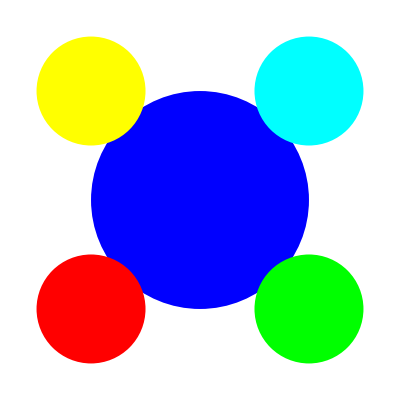

```mathematica
Show[
rendu[scene],
boudingBoxGraphics
]
```